# Math Boot Camp: Unit Vectors in Different Coordinate Systems

You can skip this boot camp if you can answer the following question:

Example
Write the polar unit vectors r̂ and θ̂ in terms of the Cartesian unit vectors x̂ and ŷ.

### Unit Vectors

We are familiar with the unit vectors in Cartesian coordinates, where x̂ points in the x-direction and ŷ points in the y-direction. Here, we will first state the general definition of a unit vector, and then extend this definition into 2D polar coordinates and 3D spherical coordinates.

#### 2D Cartesian Coordinates

Consider a point (x,y). The unit vector of the first coordinate x is defined as the vector of length 1 which points in the direction from (x,y) to (x+ⅆx,y). The vector x̂ is shown below (left) and is seen to lie along the x-direction, as expected. Similarly ŷ is defined as the unit vector pointing from (x,y) to (x,y+ⅆy) as shown below (right).

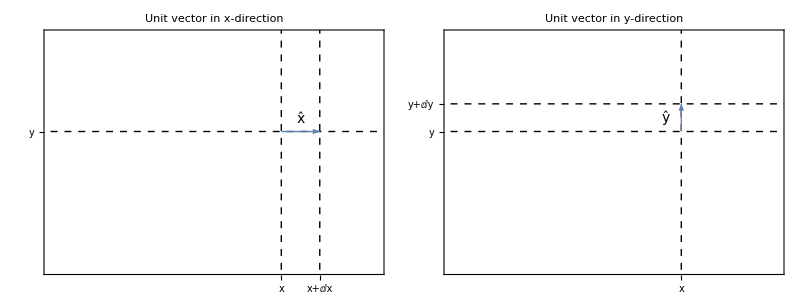

```mathematica
s=0.1;s2=0.15;
plot1=With[{x=0.6,y=0.5,dx=0.1,dy=0.1},
Show[RegionPlot[xx<0&&yy<0,{xx,0,1},{yy,0,1},PlotRange->0.85{{0,1},{0,1}},ImageSize->175,PlotRangePadding->None,FrameTicks->{{{{y,font@"y"}(*,{y+dy,font@"y+ⅆy"}*)},None},{{{x,font@"x"},{x+dx,font@"x+ⅆx"}},None}},PlotLabel->(font[#,12]&@"Unit vector in x-direction")],
Graphics[{{Dashed,Line[{{{x,0},{x,1}},{{x+dx,0},{x+dx,1}}}],Line[{{{0,y},{1,y}}(*,{{0,y+dy},{1,y+dy}}*)}]},{Thick,Arrowheads[0.05],color1,Arrow[{{x,y},{x+dx,y}}]},Text[font@"x̂",{x+dx/2,y+0.045}]}]]
];
plot2=With[{x=0.6,y=0.5,dx=0.1,dy=0.1},
Show[RegionPlot[xx<0&&yy<0,{xx,0,1},{yy,0,1},PlotRange->0.85{{0,1},{0,1}},ImageSize->200,PlotRangePadding->None,FrameTicks->{{{{y,font@"y"},{y+dy,font@"y+ⅆy"}},None},{{{x,font@"x"}(*,{x+dx,font@"x+ⅆx"}*)},None}},PlotLabel->(font[#,12]&@"Unit vector in y-direction")],
Graphics[{{Dashed,Line[{{{x,0},{x,1}}}],Line[{{{0,y},{1,y}},{{0,y+dy},{1,y+dy}}}]},{Thick,Arrowheads[0.05],color1,Arrow[{{x,y},{x,y+dy}}]},Text[font@"ŷ",{x-0.04,y+dy/2}]}]]
];
centerPlot@Grid[{{plot1,plot2}},Spacings->5,Alignment->Top]
```

#### 2D Polar Coordinates

We follow this same procedure in polar coordinates to find r̂ and θ̂. Starting from the point (r,θ), the r̂ unit vector points lies in the direction from (r,θ) to (r+ⅆr,θ), which means that it points directly outwards from the origin. Similarly, θ̂ is a unit vector pointing from (r,θ) to (r,θ+ⅆθ), which implies that θ̂ points counter-clockwise from (r,θ) along the circle of radius r. Note that in the definition of θ̂, it is critical that ⅆθ is infinitesimally small, whereas in the definition of r̂ and the definition of the Cartesian unit vectors this was not important.

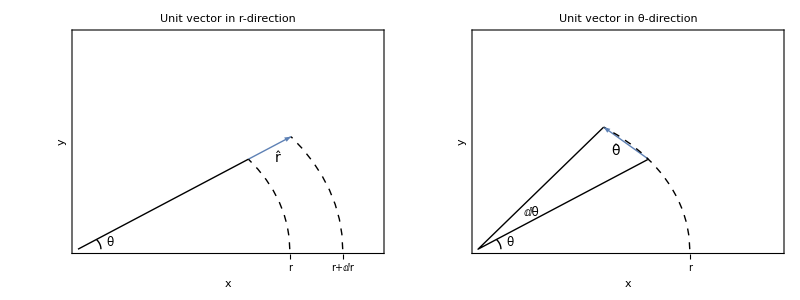

```mathematica
s=0.15;s2=0.22;r1=0.6;r2=0.75;
plot1=Show[RegionPlot[x>1,{x,0,1},{y,0,1},FrameLabel->(font[#,Italic]&/@{"x","y"}),PlotRange->0.85{{0,1},{0,1}},ImageSize->200,PlotRangePadding->None,FrameTicks->{{None,None},{{{r1 ,font["r",12]},{r2 ,font["r+ⅆr",12]}},None}},PlotLabel->(font[#,12]&@"Unit vector in r-direction")],
Graphics[{Line[{{0,0},{r1 Cos[π/4-s],r1 Sin[π/4-s]}}],Circle[{0,0},0.065,{π/4-s,0}],{Thick,color1,Arrow[{{r1 Cos[π/4-s],r1 Sin[π/4-s]},{r2 Cos[π/4-s],r2 Sin[π/4-s]}}]},{Dashed,Circle[{0,0},r1 ,{0,π/4-s}],Circle[{0,0},r2 ,{0,π/4-s}]},Text[font["θ",12],{0.09,0.028}],Text[font@"r̂",(r1+r2)/2{Cos[π/4-s2],Sin[π/4-s2]}]}]];
plot2=Show[RegionPlot[x>1,{x,0,1},{y,0,1},FrameLabel->(font[#,Italic]&/@{"x","y"}),PlotRange->0.85{{0,1},{0,1}},ImageSize->200,PlotRangePadding->None,FrameTicks->{{None,None},{{{r1 ,font["r",12]}},None}},PlotLabel->(font[#,12]&@"Unit vector in θ-direction")],
Graphics[{Line[{{r1 Cos[π/4+s],r1 Sin[π/4+s]},{0,0},{r1 Cos[π/4-s],r1 Sin[π/4-s]}}],Circle[{0,0},0.065,{π/4-s,0}],{Thick,color1,Arrow[{{r1 Cos[π/4-s],r1 Sin[π/4-s]},{r1 Cos[π/4+s],r1 Sin[π/4+s]}}]},{Dashed,Circle[{0,0},r1 ,{0,π/4+s}]},Text[font["θ",12],{0.09,0.028}],Text[font["ⅆθ",12],{0.15,0.145}],Text[font@"θ̂",0.55{Cos[π/4],Sin[π/4]}]}]];
centerPlot@Grid[{{plot1,plot2}},Spacings->5,Alignment->Top]
```

Unlike the x̂ and ŷ Cartesian coordinate unit vectors, the polar unit vectors r̂ and θ̂ depend upon the point (r,θ), although you can quickly show that they only depend upon θ and not upon r. Here are some examples:

At (r,θ)=(r,0):  r̂=x̂ and θ̂=ŷ

At (r,θ)=(r,π/2):  r̂=ŷ and θ̂=-x̂

At (r,θ)=(r,π/4):  r̂=(x̂+ŷ)/(√2) and θ̂=(x̂-ŷ)/(√2)

Now let’s find the general relations between the polar and Cartesian unit vectors.

Example
Write the polar unit vectors r̂ and θ̂ in terms of the Cartesian unit vectors x̂ and ŷ.

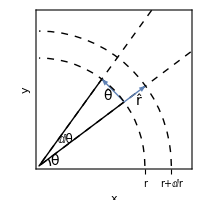

```mathematica
s=0.15;s2=0.22;r1=0.6;r2=0.75;
centerPlot@Show[RegionPlot[x>1,{x,0,1},{y,0,1},FrameLabel->(font[#,Italic]&/@{"x","y"}),PlotRange->0.85{{0,1},{0,1}},ImageSize->200,PlotRangePadding->None,FrameTicks->{{None,None},{{{r1,font["r",12]},{r2,font["r+ⅆr",12]}},None}}],
Graphics[{{Dashed,Line[{{2Cos[π/4+s],2Sin[π/4+s]},{0,0},{2Cos[π/4-s],2Sin[π/4-s]}}]},Line[{{r1 Cos[π/4+s],r1 Sin[π/4+s]},{0,0},{r1 Cos[π/4-s],r1 Sin[π/4-s]}}],Circle[{0,0},0.065,{π/4-s,0}],{Thick,color1,Arrow[{{r1 Cos[π/4-s],r1 Sin[π/4-s]},{r1 Cos[π/4+s],r1 Sin[π/4+s]}}],Arrow[{{r1 Cos[π/4-s],r1 Sin[π/4-s]},{r2 Cos[π/4-s],r2 Sin[π/4-s]}}]},{Dashed,Circle[{0,0},r1 ,{0,π/2}],Circle[{0,0},r2 ,{0,π/2}]},Text[font["ⅆθ",12],{0.15,0.145}],Text[font@"θ",{0.09,0.028}],Text[font@"θ̂",0.55{Cos[π/4],Sin[π/4]}],Text[font@"r̂",(r1+r2)/2{Cos[π/4-s2],Sin[π/4-s2]}]}]]
```

Solution
The geometrical approach is easiest. Since r̂ points along the line containing the origin and the point (r,θ), its components must be

r̂=Cos[θ]x̂+Sin[θ]ŷ

θ̂ points 90° counter-clockwise of r̂, which implies

θ̂=-Sin[θ]x̂+Cos[θ]ŷ

As a double check, note that both r̂ and θ̂ are unit vectors (i.e. have norm 1), the two unit vectors are perpendicular (r̂·θ̂=0), and in the limit θ=0 we regain r̂=x̂ and θ̂=ŷ, so that θ̂ points in the correct direction relative to r̂. □

Using polar coordinates will greatly simplify problems that have circular geometries (for example, a particle undergoing uniform circular motion). However, when using any coordinate system other than Cartesian coordinates, you must remember that the unit vectors r̂ and θ̂ can vary in time (if the base point about which they are computed changes in time). To find how these unit vectors vary with time, we differentiate Equations (TextNumbered) and (TextNumbered) with respect to time, using the chain rule and the fact that for Cartesian coordinates (ⅆ x̂)/ⅆt=(ⅆ ŷ)/ⅆt=0 irrespective of the base point,

(ⅆ r̂)/ⅆt=-θ̇Sin[θ]x̂+θ̇ Cos[θ]ŷ=θ̇ θ̂

(ⅆ θ̂)/ⅆt=-θ̇Cos[θ]x̂-θ̇ Sin[θ]ŷ=-θ̇ r̂

Fantastic! Now we are ready to calculate v⃗. The position vector using polar unit vectors has the very simple form

r⃗=r r̂

Differentiating with respect to time, we obtain the velocity

v⃗=(ⅆ r⃗)/ⅆt
=ṙ r̂+r (ⅆ r̂)/ⅆt
=ṙ r̂+r θ̇ θ̂

In other words, v⃗=v_r r̂+v_θ θ̂ where v_r=ṙ is the velocity in the radial direction and v_θ=r θ̇ is the velocity in the θ̂ direction.

#### 3D Spherical Coordinates

We extend procedure above to determine the spherical coordinate unit vectors r̂, ϕ̂, and θ̂. As shown below, r̂ points radially outward, ϕ̂ points in the x-y plane along the polar angle, and θ̂ points in the azimuthal direction.

```mathematica
centerPlot@Manipulate[
point={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
{vec1,vec2,vec3}={{point,1.4point},{point,point+0.4{-Sin[ϕ],Cos[ϕ],0}},{point,point+0.4{Cos[θ]Cos[ϕ],Cos[θ]Sin[ϕ],-Sin[θ]}}};
{label1,label2,label3}=0.3(#[[2]]-#[[1]])+#[[2]]&/@{vec1,vec2,vec3};
Graphics3D[{Opacity[0.6],Sphere[],Opacity[1],Arrow[1.2{{{0,0,0},{1,0,0}},{{0,0,0},{0,1,0}},{{0,0,0},{0,0,1}}}],Line[{{0,0,0},point}],color1,Arrow[{vec1,vec2,vec3}],Text[font["r̂",16,Bold],label1],Text[font["ϕ̂",16,Bold],label2],Text[font["θ̂",16,Bold],label3],Purple,PointSize[0.02],Point[point],Black,Text[font["x",Italic],{1.3,0,0}],Text[font["y",Italic],{0,1.3,0}],Text[font["z",Italic],{0,0,1.3}]},Boxed->False,ViewAngle->0.3180076292247497,ViewCenter->{{0.5,0.5,0.5},{0.503,0.492}},ViewPoint->{3.175,0.753,0.895},ViewVertical->{0.,0.,1.},PlotLabel->font@"Spherical coordinate unit vectors",ImageSize->{208,230.6}],{{ϕ,π/4},0,2π},{{θ,π/3},0,π}]
```

Note that the unit vectors are all orthogonal to each other, and that the coordinate system is right handed. In the language of the cross product, this implies that r̂×θ̂=ϕ̂ (similar to how in Cartesian coordinates x̂×ŷ=ẑ).

As a fun exercise, you can show that the spherical coordinate unit vectors are related to the Cartesian coordinate vectors by

r̂=Sin[θ]Cos[ϕ]x̂+Sin[θ]Sin[ϕ]ŷ+Cos[θ]ẑ
θ̂=Cos[θ]Cos[ϕ]x̂+Cos[θ]Sin[ϕ]ŷ-Sin[θ]ẑ
ϕ̂=-Sin[ϕ]x̂+Cos[ϕ]ŷ

You will find in Ph 1b that descriptions of spherically symmetric setups are much simpler in terms of these unit vectors. For example, we will see next term that the Coulomb force from a point charge q exerts an electric field E with magnitude

E=(k q)/r^2

which points in the radial direction. In Cartesian coordinates, we would express this relation as

E⃗=(k q)/(x^2+y^2+z^2)(x x̂+y ŷ+z ẑ)/((x^2+y^2+z^2)^(1/2))

In contrast, in spherical coordinates this equation takes the more compact form

E⃗=(k q)/r^2 r̂

#### 3D Cylindrical Coordinates

When problems have cylindrical symmetry, it is often easiest to work in cylindrical coordinates. Given a point (ρ,θ,z) shown in the diagram below, what are the cylindrical coordinate vectors ρ̂, θ̂, and ẑ in terms of the Cartesian coordinate unit vectors?

```mathematica
arc[r_,θ_,{ϕ1_, ϕ2_}]:=
Line[Table[r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]},{ϕ,ϕ1,ϕ2,(ϕ2-ϕ1)/Round[((ϕ2-ϕ1)/(2π))180.]}]]
arc[r_,{θ1_,θ2_},ϕ_]:=
Line[Table[r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]},{θ,θ1,θ2,(θ2-θ1)/Round[((θ2-θ1)/(2π))180.]}]]
PolarToCartesian[{r_,θ_,ϕ_}]:=
r{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], Cos[ϕ]}
cylindricalGraphic = With[{
al=1.2,
tl=1.35,
height=0.85
},
cyl1 = First[ParametricPlot3D[
{0.8 Sin[ϕ] Cos[θ],0.8 Sin[ϕ] Sin[θ], height},{ϕ,0,π/2},{θ,0,2π},Boxed->False,Mesh->None,Axes->None]];
cyl2 = First[ParametricPlot3D[
{0.8 Cos[θ],0.8 Sin[θ],zz},{zz,0,height},{θ,0,2π},Boxed->False,Mesh->None,Axes->None]];
centerPlot@Graphics3D[{
Arrowheads[Medium],
Arrow[al{{{-1,0,0},{1,0,0}},{{0,-1,0},{0,1,0}},{{0,0,-.1/1.1},{0,0,1}}}],
Text[font["x",Italic],tl{1,0,0}],
Text[font["y",Italic],tl{0,1,0}],
Text[font["z",Italic],tl{0,0,1}],
With[{θ=45°,ar=.25,tr=.25,z=0.35,ρ=0.65},
{
PointSize[0.02],{RGBColor[0.32, 0., 0.51],Point[0.99{ρ Cos[θ],ρ Sin[θ],z}]},
arc[ρ,{0,θ},π/2],Line[{{{0,0,z},{ρ Cos[θ],ρ Sin[θ],z}},{{0,0,0},{ρ Cos[θ],ρ Sin[θ],0}},{{ρ Cos[θ],ρ Sin[θ],0},{ρ Cos[θ],ρ Sin[θ],z}}}],
arc[ar,{0,θ},π/2],
Text[font@"θ",{tr Cos[θ/2],tr Sin[θ/2],0}+{0,0,0.035},{-1,1}],
Text[font["z",Italic],{(ρ+0.08) Cos[θ],(ρ+0.08) Sin[θ],z/2}+{0,0,0.04}],
Text[font["ρ"],{ρ/2 Cos[θ],ρ/2 Sin[θ],z}+{0,0,0.0},{0,-1}]
}],
{Opacity[.7],cyl1,cyl2}
},Boxed->False,ViewPoint->{2.8787694864121054,-0.8743808538009489,1.501014445836184},ViewVertical->{0.022146876875507985,-0.006437778851452326,1.7471986729777156},ImageSize->250]
]
```

-Graphics3D-

This question is straightforward if we realize that cylindrical coordinates are equivalent to 2D polar coordinates with the Cartesian z-coordinate tacked on. This implies that the cylindrical coordinate unit vectors are given by Equations (TextNumbered) and (TextNumbered) as

r̂=Cos[θ]x̂+Sin[θ]ŷ

θ̂=-Sin[θ]x̂+Cos[θ]ŷ

Meanwhile, the z-coordinate is identical to the Cartesian z-coordinate, so its corresponding unit vector is trivially

ẑ=ẑ

irrespective of the base point (ρ,θ,z).

## Mathematica Initialization

```mathematica
colors={color1,color2,color3,color4}=ColorData[97][#]&/@{1,10,5,6};
```

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```